```mathematica
<<Notation`
```

```mathematica
Symbolize[Subscript[x_, y_]];
```

```mathematica
ClearAll[C2,I1,I2,I3,I4,I5,λ2,λ,γ,Subscript[P, 2]]
```

```mathematica
Block[{ω =1 ,Subscript[R, 0]=1,Subscript[a, 0]=0,Subscript[a, n]=0,Subscript[b, n]=1.,n=1,G = 10^5,ρ=10^3,Nf=10},
AngularAcc[t_]=Subscript[R, 0](Subscript[a, 0]+Subscript[a, n] Cos[2π n ω t]+Subscript[b, n] Sin[2π n ω t]);
(*R  =r/Subscript[R, 0];
T =2π n ω t;*)
C2 = G/ρ/(2π Subscript[R, 0] n ω)^2;γ[i_]:=BesselJZero[1,i];
I1[i_]:=- Subscript[A, n](C2 γ[i]^2-1 );
I2[i_]:=- Subscript[B, n](C2 γ[i]^2-1 );
I3[i_]:=(Subscript[A, n]+Subscript[A, 0])(C2 γ[i]^2-1 )+Subscript[A, 0](1-C2 γ[i]^2)/(C2 γ[i]^2);
I4[i_]:= Subscript[B, n](C2 γ[i]^2-1 );
I5[i_]:= -Subscript[A, 0]((C2 γ[i]^2-1 )^2)/(C2 γ[i]^2);
λ2[i_]:= C2 γ[i]^2;
λ[i_]=Sqrt[λ2[i]];
Subscript[P, 2][R_,i_] := (-2 BesselJ[1,R γ[i]])/(γ[i] BesselJ[0,γ[i]](C2 γ[i]^2-1)^2);
Subscript[A, n]= (Subscript[a, n] Subscript[R, 0])/(2π n ω)^2;
Subscript[B, n]= (Subscript[b, n] Subscript[R, 0])/(2π n ω)^2;
Subscript[A, 0]=(Subscript[a, n] Subscript[R, 0])/(2π n ω)^2;
V[R_,T_]=N@Sum[Subscript[P, 2][R,i](I1[i] Cos[T]+I2[i] Sin[T]+I3[i] Cos[λ[i] T]+I4[i]/λ[i] Sin[λ[i]T]+I5[i]),{i,Nf} ];
uRB[R_,T_]=(Subscript[A, 0] R T^2)/2+Subscript[B, n] R T + Subscript[A, n] R -Subscript[A, n] R Cos[T]-Subscript[B, n] R Sin[T];
u[R_,T_]=V[R,T]+uRB[R,T];
u1[T_]=(Subscript[A, 0]  T^2)/2+Subscript[B, n] T + Subscript[A, n] -Subscript[A, n] Cos[T]-Subscript[B, n]  Sin[T];
(*V1[T_]=N@V[0.35,T];*)
(*Plot[AngularAcc[T],{T,0,1/(2π)}]*)
(*Plot[V1[T],{T,0,2π}]*)
{u1[T]-u[1,T],u[0,T],u[R,0],D[u[R,T],T]/.T->0};
Residual[R_,T_]=D[u[R,T],{T,2}]-C2(D[u[R,T],{R,2}]+D[u[R,T],R]/R-u[R,T]/R^2)//Simplify;
Plot3D[Residual[R,T],{R,0,1},{T,0,2π}]
]
```

-Graphics3D-

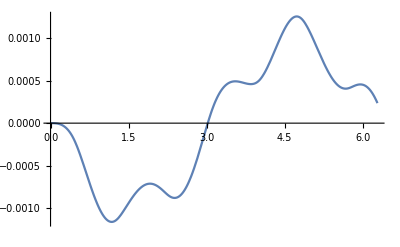

```mathematica
p1 = Plot[V[0.5,T],{T,0,2π}]
```

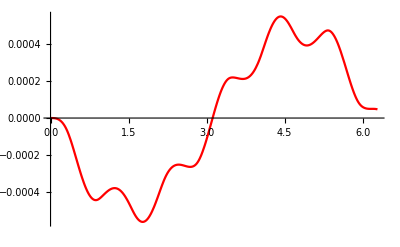

```mathematica
p2 = Plot[V[0.5,T],{T,0,2π},PlotStyle->Red]
```

```mathematica
Block[{ω =1 ,Subscript[R, 0]=1,Subscript[a, 0]=0,Subscript[a, n]=0,Subscript[b, n]=1.,n=1,G = 10^5,ρ=10^3,Nf=10},
C2 = G/(2ρ)/(2π Subscript[R, 0] n ω)^2;
γ[i_]:=BesselJZero[1,i];
I1[i_]:=- Subscript[A, n](C2 γ[i]^2-1 );
I2[i_]:=- Subscript[B, n](C2 γ[i]^2-1 );
I3[i_]:=(Subscript[A, n]+Subscript[A, 0])(C2 γ[i]^2-1 )+Subscript[A, 0](1-C2 γ[i]^2)/(C2 γ[i]^2);
I4[i_]:= Subscript[B, n](C2 γ[i]^2-1 );
I5[i_]:= -Subscript[A, 0]((C2 γ[i]^2-1 )^2)/(C2 γ[i]^2);
λ2[i_]:= C2 γ[i]^2;
λ[i_]=Sqrt[λ2[i]];
Subscript[P, 2][R_,i_] := (-2 BesselJ[1,R γ[i]])/(γ[i] BesselJ[0,γ[i]](C2 γ[i]^2-1)^2);
Subscript[A, n]= (Subscript[a, n] Subscript[R, 0])/(2π n ω)^2;
Subscript[B, n]= (Subscript[b, n] Subscript[R, 0])/(2π n ω)^2;
Subscript[A, 0]=(Subscript[a, n] Subscript[R, 0])/(2π n ω)^2;
uRB[R_,T_]=(Subscript[A, 0] R T^2)/2+Subscript[B, n] R T + Subscript[A, n] R -Subscript[A, n] R Cos[T]-Subscript[B, n] R Sin[T];
(*Ωpp[t_]=1000 Cos[ 500 t];*)
uSol=NDSolve[{
1/r^2 C2  (-u1[r,t]+r (Derivative[1,0][u1][r,t]+r Derivative[2,0][u1][r,t])) ==Derivative[0,2][u1][r,t],
u1[r,0]==0,
Derivative[0,1][u1][r,0]==0,
u1[1.,t]==(Subscript[A, 0]  t^2)/2+Subscript[B, n] t + Subscript[A, n] -Subscript[A, n] Cos[t]-Subscript[B, n]  Sin[t]
},u1,{r,0.000001,1.},{t,0,2π},AccuracyGoal->5]
]
```

{{u1→InterpolatingFunction[…]}}

```mathematica
u2[R_,T_]=u1[R,T]/.uSol[[1]]
```

InterpolatingFunction[…][R,T]

```mathematica
u2[1,1]
```

0.00402674

```mathematica
Residual2[R_,T_]=D[u2[R,T],{T,2}]-C2(D[u2[R,T],{R,2}]+D[u2[R,T],R]/R-u2[R,T]/R^2)//Simplify;
Plot3D[Residual2[R,T],{R,0,1},{T,0,2π},PlotRange->All]
```

-Graphics3D-

-0.0253303 R T+0.0253303 R Sin[T]+InterpolatingFunction[…][R,T]

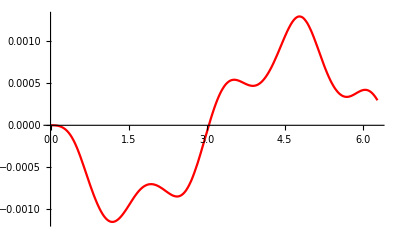

```mathematica
V1[R_,T_]=(u1[R,T]/.uSol[[1]])-uRB[R,T]
p2= Plot[V1[0.5,T],{T,0,2π},PlotStyle->Red]
```

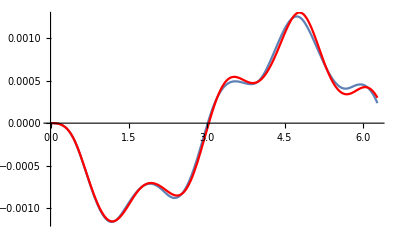

```mathematica
Show[p1,p2]
```

## Our solution

```mathematica
Block[{ μ=10^5,ρ=10^3,n=1,ω=1
(*,c,Ωpp,γ,λ,f,g,FCC,BJC,B,A,a,u,v*)},
R1=1.;
r0  =0.000001;
tend=2π;
Subscript[c, s]=Sqrt[μ/(2ρ)];
(*Ωpp[t_]=Piecewise[{{1000 Sin[ 100 t],0≤t≤π/100.},{0,t>π/100.}}];*)
ΩppReal[t_]= 1/2. Sin[2π n ω t];
(*Ωpp[t_]=1000 Cos[ 500 t];*)
uθNSol=NDSolve[{
1/r^2 Subscript[c, s]^2 (-uθ[r,t]+r (Derivative[1,0][uθ][r,t]+r Derivative[2,0][uθ][r,t]))-r ΩppReal[t] ==Derivative[0,2][uθ][r,t],
uθ[r,0]==0,
Derivative[0,1][uθ][r,0]==0,
uθ[R1,t]==0
},uθ,{r,r0,R1},{t,0,1},AccuracyGoal->6]
]
```

NDSolve::eerr: Warning: scaled local spatial error estimate of 48.3815 at t = 1. in the direction of independent variable r is much greater than the prescribed error tolerance. Grid spacing with 25 points may be too large to achieve the desired accuracy or precision. A singularity may have formed or a smaller grid spacing can be specified using the MaxStepSize or MinPoints method options.

{{uθ→InterpolatingFunction[…]}}

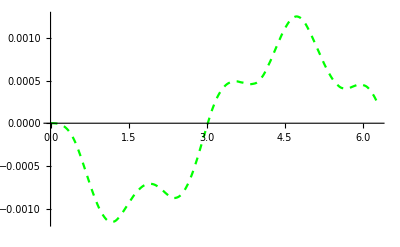

```mathematica
p3 =Plot[2uθ[0.5,t/(2π)]/.uθNSol[[1]],{t,0.0,2π},PlotStyle->Directive[Green,Dashed]]
```

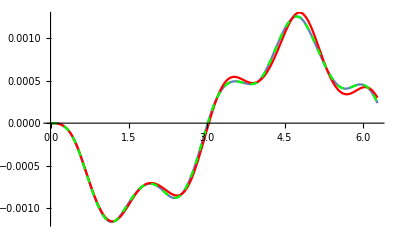

```mathematica
Show[p1,p2,p3]
```

```mathematica
Block[{MM = 10,NN=10(*,λ =8500*),T =10 , μ=10^5,ρ=10^3,ω=1,R1 = 1,r0=0.00001
,Subscript[c, s],Subscript[τ, c],Ωpp,γ,λ,f,g,FSC,BJC,B,A,a,sol},
Subscript[c, s]=Sqrt[μ/ρ];
Subscript[τ, c] = R1/Subscript[c, s];
ΩppReal[t_]=1. Sin[2π  ω t];
Ωpp[τ_]=ΩppReal[τ Subscript[τ, c]] Subscript[τ, c]^2;
γ[m_]=N@BesselJZero[1,m];
λ[n_]=(2.0π n Subscript[τ, c])/T;
f[n_]=Sin[λ[n] #2]&;
g[m_]:=Sqrt[2] BesselJ[1,#1  γ[m]]/BesselJ[0,γ[m]]&;
FSC[n_]:=FourierSinCoefficient[Ωpp[τ],τ,n,FourierParameters->{1,2.0π Subscript[τ, c]/T}];
(*FSC/@Range[10]*)
BJC[m_]:=NIntegrate[g[m][R] R^2,{R,0,1}];
B[m_,n_]:=-BJC[m]FSC[n];
A[m_,n_]:=B[m,n]/(γ[m]^2-λ[n]^2);
a[m_]:=Sum[A[m,n]λ[n],{n,NN}]/( γ[m]);
u[R_,τ_]=Sum[ g[m][R,τ] Sum[A[m,n]f[n][R,τ],{n,NN}],{m,MM}];
v[R_,τ_]=Sum[-a[m] g[m][R,τ] Sin[ γ[m]τ],{m,MM}];
sol[R_,τ_]=Chop[Simplify[u[R,τ]+v[R,τ]],10^-7];
RealSol[R_,τ_] = R1 sol[R/R1 ,τ/Subscript[τ, c] ]
]
```

-0.00090708 BesselJ[1,3.83171 R] Sin[6.28319 τ]+0.000194557 BesselJ[1,7.01559 R] Sin[6.28319 τ]-0.0000763582 BesselJ[1,10.1735 R] Sin[6.28319 τ]+0.0000388107 BesselJ[1,13.3237 R] Sin[6.28319 τ]-0.0000228163 BesselJ[1,16.4706 R] Sin[6.28319 τ]+0.0000147309 BesselJ[1,19.6159 R] Sin[6.28319 τ]-0.0000101541 BesselJ[1,22.7601 R] Sin[6.28319 τ]+7.34621×10^-6 BesselJ[1,25.9037 R] Sin[6.28319 τ]-5.51624×10^-6 BesselJ[1,29.0468 R] Sin[6.28319 τ]+4.26621×10^-6 BesselJ[1,32.1897 R] Sin[6.28319 τ]+0.000148742 BesselJ[1,3.83171 R] Sin[38.3171 τ]-0.0000174246 BesselJ[1,7.01559 R] Sin[70.1559 τ]+4.71592×10^-6 BesselJ[1,10.1735 R] Sin[101.735 τ]-1.83023×10^-6 BesselJ[1,13.3237 R] Sin[133.237 τ]+8.70393×10^-7 BesselJ[1,16.4706 R] Sin[164.706 τ]-4.71847×10^-7 BesselJ[1,19.6159 R] Sin[196.159 τ]+2.80317×10^-7 BesselJ[1,22.7601 R] Sin[227.601 τ]-1.78189×10^-7 BesselJ[1,25.9037 R] Sin[259.037 τ]+1.19323×10^-7 BesselJ[1,29.0468 R] Sin[290.468 τ]

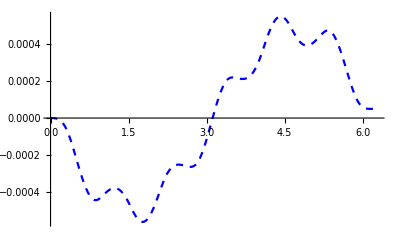

```mathematica
p4 =Plot[RealSol[0.5,t/(2π)],{t,0.0,2π},PlotStyle->Directive[Blue,Dashed]]
```

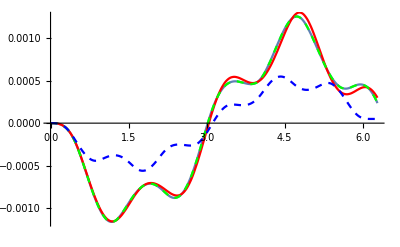

```mathematica
Show[p1,p2,p3,p4]
```

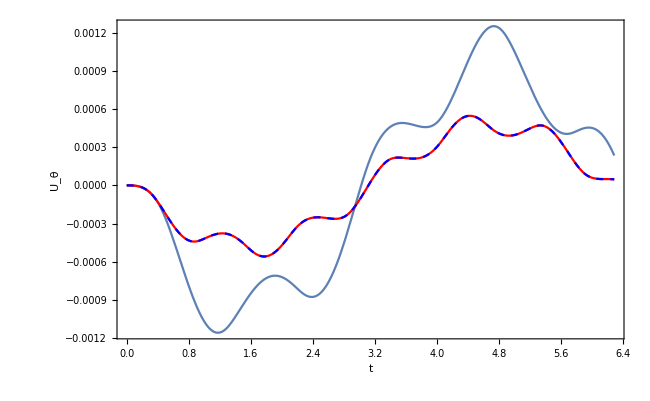

```mathematica
Show[p1,p2,p4,ImageSize->Large,GridLines->None,Axes->False,AxesStyle->Directive[Black,FontFamily->"Times",24],Frame->True,FrameStyle->Directive[FontFamily->"Times",20],FrameLabel->{Style["t",Black,FontFamily->"Times",24],Style["U_θ",Black,FontFamily->"Times",24]},RotateLabel->False]
```